```mathematica
ψ1=(2 An ⅇ^((ⅈ (4 a k n π x z0-4 n^2 π^2 z z0+a^2 k^2 (x^2+y^2+2 (z+z0)^2)))/(2 a^2 k (z+z0))) π ψ0)/(k (z+z0) λ);
ψ1=(2 An ⅇ^((ⅈ (4 a k n π x z0-4 n^2 π^2 z z0+a^2 k^2 (x^2+y^2+2 (z+z0)^2)))/(2 a^2 k (z+z0))) π ψ0)/(k λ);
```

#### Set the Fourier coefficients to the Heaviside function

```mathematica
f = ( HeavisideTheta[x + 1/40] - HeavisideTheta[x - 1/40]);
```

```mathematica
A[n_] = Integrate[f Exp[-2 ⅈ π n x],{x,-1/2,1/2}]
```

Sin[(n π)/20]/(n π)

```mathematica
A0 = Integrate[f,{x,-1/2,1/2}]
```

1/20

20

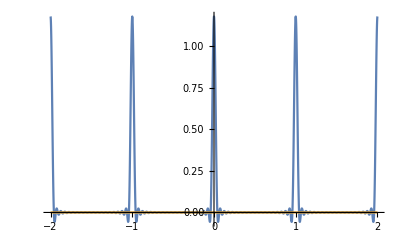

```mathematica
num = 20
t = A[n] Exp[2 ⅈ π n x];
tS = Sum[t,{n,-num,-1}] +A0+ Sum[t,{n,1,num}];
Plot[{Re[tS],Im[tS]},{x,-2,2},PlotRange->Full]
```

```mathematica
12
```

12

```mathematica
ψS =Sum[ψ1 /. An -> A[n],{n,-num,-1}]+( ψ1/. n-> 0/. An -> A0)+Sum[ψ1 /. An-> A[n],{n,1,num}];
```

```mathematica
vals = {y->0, k->( 2π / λ), λ-> 10^-3,a-> 1, z0->5 10^3,ψ0-> 1};
```

```mathematica
ψS2 =Abs[ψS/. vals /. vals]^2 //Simplify;
```

```mathematica
plt = DensityPlot[ψS2,{z,0,4000},{x,-3,3},PlotPoints->800,ColorFunction->"Rainbow",ImageSize->{2048,2048}];
```

```mathematica
Export["plot.png",plt]
```

plot.png